## This notebook, calculates the frequency of a charged massles scalar field around a RN black hole considering a mirror: based on Phys Rev D 70 044039 (2004). Aveiro 20 feb 2013. check: mirrorFreq.mw

```mathematica
Exit
```

```mathematica
Clear; MaxExtraPrecision=100;
M=1;l=1; mu=0.1; qscal=0.25; Q=0.95;
```

```mathematica
winit=(0.15-0.00005*I)
```

0.15-0.00005 ⅈ

```mathematica
(*Define the Function of w as the solution of the Diferential equation given a value of r1, the position of the mirror. The returning value is the solution evaluated at r1 *)
```

```mathematica
LeavP1[w_?NumberQ]:=
Module[{Res},
r0=rp+10^(-8);r1=30; rm=M-Sqrt[M^2-Q^2]; rp=M+Sqrt[M^2-Q^2] ;wc=qscal*Q/rp;
qsol=-Sqrt[mu*mu-w*w] ;
rhosol=-I*rp^2*(w-wc)/(rp-rm);
sigmasol=(qscal*Q*w+M*mu^2-2*M*w^2);
sol=NDSolve[{(1-2*M/r+Q^2/r^2)*D[Rs[r],{r,2}]+(   2/r*( 1-2*M/r+Q^2/r^2) + (  2*M/r^2-2*Q^2/r^3  ) )*D[Rs[r],{r,1}]+(     1/(1-2*M/r+Q^2/r^2)*(  w-qscal*Q/r )^2-l*(l+1)/r^2-mu^2        )*Rs[r]==0,Rs[r0]==(rp-rm)^(sigmasol-rhosol-1)*Exp[qsol*r0]*(r0-rp)^(rhosol),Rs'[r0]==(rp-rm)^(sigmasol-rhosol-1)*Exp[qsol*r0]*(rhosol)*(r0-rp)^(rhosol-1)},Rs,{r,r0,r1},
          MaxSteps->50000];
Res=Rs[r1]/.sol];
```

```mathematica
(*Find the root of this function, this w is such as the value of the function is zero at *)
```

```mathematica
wres=FindRoot[LeavP1[w]==0,{w,winit}] [[1]][[2]]
```

0.180285+1.39296×10^-9 ⅈ

```mathematica
(*Check that the solution obtained is the solution wanted and plot it*)
```

```mathematica
r0=rp+10^(-8);r1=30; rm=M-Sqrt[M^2-Q^2]; rp=M+Sqrt[M^2-Q^2] ; wc=qscal*Q/rp
qsol=-Sqrt[mu*mu-wres*wres] ;
rhosol=-I*rp^2*(wres-wc)/(rp-rm);
sigmasol=(qscal*Q*wres+M*mu^2-2*M*wres^2);
(*potsol= 1/f*(  w-qscal*Q/r )^2-l*(l+1)/r^2-mu^2;*)
sol=NDSolve[{(1-2*M/r+Q^2/r^2)*D[Rs[r],{r,2}]+(   2/r*( 1-2*M/r+Q^2/r^2) + (  2*M/r^2-2*Q^2/r^3  ) )*D[Rs[r],{r,1}]+(     1/(1-2*M/r+Q^2/r^2)*(  wres-qscal*Q/r )^2-l*(l+1)/r^2-mu^2        )*Rs[r]==0,Rs[r0]==(rp-rm)^(sigmasol-rhosol-1)*Exp[qsol*r0]*(r0-rp)^(rhosol),Rs'[r0]==(rp-rm)^(sigmasol-rhosol-1)*Exp[qsol*r0]*(rhosol)*(r0-rp)^(rhosol-1)},Rs,{r,r0,r1},
          MaxSteps->50000];
```

0.180987

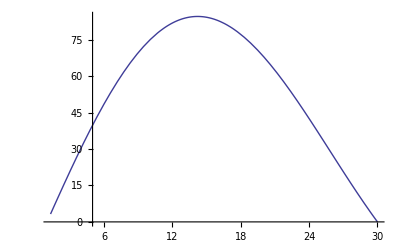

```mathematica
Plot[{2.01*Abs[Rs[r]/.sol]},{r,rp,r1}]
```

```mathematica
(*Now, do the previous procedure for several values of r1, the position of the mirror:
I approach the value from right and left because dont know the rate of change in the function,    in some cases is very high and then fails from one step to other.*)
```

```mathematica
winit=(0.15+0.000005*I);
ie=0;While[ie<151,NITMAX=250;
LeavP1[w_?NumberQ]:=
Module[{Res},
r0=rp+10^(-8);r1=30+ie/5; rm=M-Sqrt[M^2-Q^2]; rp=M+Sqrt[M^2-Q^2] ;wc=qscal*Q/rp;
qsol=-Sqrt[mu*mu-w*w] ;
rhosol=-I*rp^2*(w-wc)/(rp-rm);
sigmasol=(qscal*Q*w+M*mu^2-2*M*w^2);

sol=NDSolve[{(1-2*M/r+Q^2/r^2)*D[Rs[r],{r,2}]+(   2/r*( 1-2*M/r+Q^2/r^2) + (  2*M/r^2-2*Q^2/r^3  ) )*D[Rs[r],{r,1}]+(     1/(1-2*M/r+Q^2/r^2)*(  w-qscal*Q/r )^2-l*(l+1)/r^2-mu^2        )*Rs[r]==0,Rs[r0]==(rp-rm)^(sigmasol-rhosol-1)*Exp[qsol*r0]*(r0-rp)^(rhosol),Rs'[r0]==(rp-rm)^(sigmasol-rhosol-1)*Exp[qsol*r0]*(rhosol)*(r0-rp)^(rhosol-1)},Rs,{r,r0,r1},
          MaxSteps->50000];
Res=Rs[r1]/.sol];
wres=FindRoot[LeavP1[w]==0,{w,winit}] [[1]][[2]];
witer[ie]=wres;
radit[ie]=r1;
winit=wres-0.001;
ie=ie+1
]
t1r=Table[{N[radit[n],10],Re[witer[n]]},{n,0,150}];
t2r=Table[{N[radit[n],10],Im[witer[n]]},{n,0,150}]
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot :: lstol will be suppressed during this calculation.

{{30.,1.39216×10^-9},{30.2,2.78151×10^-9},{30.4,4.05594×10^-9},{30.6,5.2288×10^-9},{30.8,6.31389×10^-9},{31.,7.29986×10^-9},{31.2,8.20354×10^-9},{31.4,9.03386×10^-9},{31.6,9.78974×10^-9},{31.8,1.04785×10^-8},{32.,1.11024×10^-8},{32.2,1.16723×10^-8},{32.4,1.21879×10^-8},{32.6,1.26522×10^-8},{32.8,1.30702×10^-8},{33.,1.3444×10^-8},{33.2,1.37776×10^-8},{33.4,1.4074×10^-8},{33.6,1.43352×10^-8},{33.8,1.45644×10^-8},{34.,1.47624×10^-8},{34.2,1.49331×10^-8},{34.4,1.50849×10^-8},{34.6,1.51979×10^-8},{34.8,1.52956×10^-8},{35.,1.53729×10^-8},{35.2,1.54302×10^-8},{35.4,1.54706×10^-8},{35.6,1.54933×10^-8},{35.8,1.55008×10^-8},{36.,1.54944×10^-8},{36.2,1.54744×10^-8},{36.4,1.54426×10^-8},{36.6,1.53997×10^-8},{36.8,1.53467×10^-8},{37.,1.52831×10^-8},{37.2,1.52116×10^-8},{37.4,1.513×10^-8},{37.6,1.50448×10^-8},{37.8,1.49525×10^-8},{38.,1.4851×10^-8},{38.2,1.47503×10^-8},{38.4,1.46363×10^-8},{38.6,1.45193×10^-8},{38.8,1.44002×10^-8},{39.,1.42776×10^-8},{39.2,1.41499×10^-8},{39.4,1.40197×10^-8},{39.6,1.38877×10^-8},{39.8,1.37536×10^-8},{40.,1.36154×10^-8},{40.2,1.34839×10^-8},{40.4,1.33356×10^-8},{40.6,1.31946×10^-8},{40.8,1.30534×10^-8},{41.,1.29093×10^-8},{41.2,1.2765×10^-8},{41.4,1.26195×10^-8},{41.6,1.24714×10^-8},{41.8,1.23302×10^-8},{42.,1.21828×10^-8},{42.2,1.20387×10^-8},{42.4,1.18944×10^-8},{42.6,1.17495×10^-8},{42.8,1.16028×10^-8},{43.,1.14612×10^-8},{43.2,1.13154×10^-8},{43.4,1.11727×10^-8},{43.6,1.10261×10^-8},{43.8,1.08918×10^-8},{44.,1.07508×10^-8},{44.2,1.06123×10^-8},{44.4,1.04743×10^-8},{44.6,1.03345×10^-8},{44.8,1.01994×10^-8},{45.,1.00659×10^-8},{45.2,9.93208×10^-9},{45.4,9.79958×10^-9},{45.6,9.66836×10^-9},{45.8,9.53827×10^-9},{46.,9.40917×10^-9},{46.2,9.28033×10^-9},{46.4,9.15606×10^-9},{46.6,9.03613×10^-9},{46.8,8.90681×10^-9},{47.,8.77251×10^-9},{47.2,8.66391×10^-9},{47.4,8.54452×10^-9},{47.6,8.42827×10^-9},{47.8,8.31181×10^-9},{48.,8.19705×10^-9},{48.2,8.08324×10^-9},{48.4,7.9696×10^-9},{48.6,7.85877×10^-9},{48.8,7.75083×10^-9},{49.,7.643×10^-9},{49.2,7.53612×10^-9},{49.4,7.43071×10^-9},{49.6,7.32499×10^-9},{49.8,7.22448×10^-9},{50.,7.12277×10^-9},{50.2,7.02218×10^-9},{50.4,6.92504×10^-9},{50.6,6.82658×10^-9},{50.8,6.73225×10^-9},{51.,6.63638×10^-9},{51.2,6.54457×10^-9},{51.4,6.45261×10^-9},{51.6,6.36196×10^-9},{51.8,6.27276×10^-9},{52.,6.18319×10^-9},{52.2,6.0977×10^-9},{52.4,6.01208×10^-9},{52.6,5.92765×10^-9},{52.8,5.84433×10^-9},{53.,5.74839×10^-9},{53.2,5.68135×10^-9},{53.4,5.60176×10^-9},{53.6,5.52307×10^-9},{53.8,5.43652×10^-9},{54.,5.37819×10^-9},{54.2,5.29387×10^-9},{54.4,5.22021×10^-9},{54.6,5.14679×10^-9},{54.8,5.07432×10^-9},{55.,5.00349×10^-9},{55.2,4.93407×10^-9},{55.4,4.86628×10^-9},{55.6,4.79741×10^-9},{55.8,4.73096×10^-9},{56.,4.6648×10^-9},{56.2,4.59936×10^-9},{56.4,4.51961×10^-9},{56.6,4.47525×10^-9},{56.8,4.41065×10^-9},{57.,4.34956×10^-9},{57.2,4.28911×10^-9},{57.4,4.22036×10^-9},{57.6,4.17226×10^-9},{57.8,4.1145×10^-9},{58.,4.05748×10^-9},{58.2,4.00122×10^-9},{58.4,3.95235×10^-9},{58.6,3.89228×10^-9},{58.8,3.83807×10^-9},{59.,3.78618×10^-9},{59.2,3.73389×10^-9},{59.4,3.68349×10^-9},{59.6,3.63291×10^-9},{59.8,3.58277×10^-9},{60.,3.53446×10^-9}}

```mathematica
(*Calculate the values leftward*)
```

```mathematica
winit=(0.15+0.000005*I);
ie=0;While[ie<101,NITMAX=250;
LeavP1[w_?NumberQ]:=
Module[{Res},
r0=rp+10^(-8);r1=30-ie/5; rm=M-Sqrt[M^2-Q^2]; rp=M+Sqrt[M^2-Q^2] ;wc=qscal*Q/rp;
qsol=-Sqrt[mu*mu-w*w] ;
rhosol=-I*rp^2*(w-wc)/(rp-rm);
sigmasol=(qscal*Q*w+M*mu^2-2*M*w^2);
(*potsol= 1/f*(  w-qscal*Q/r )^2-l*(l+1)/r^2-mu^2;*)
sol=NDSolve[{(1-2*M/r+Q^2/r^2)*D[Rs[r],{r,2}]+(   2/r*( 1-2*M/r+Q^2/r^2) + (  2*M/r^2-2*Q^2/r^3  ) )*D[Rs[r],{r,1}]+(     1/(1-2*M/r+Q^2/r^2)*(  w-qscal*Q/r )^2-l*(l+1)/r^2-mu^2        )*Rs[r]==0,Rs[r0]==(rp-rm)^(sigmasol-rhosol-1)*Exp[qsol*r0]*(r0-rp)^(rhosol),Rs'[r0]==(rp-rm)^(sigmasol-rhosol-1)*Exp[qsol*r0]*(rhosol)*(r0-rp)^(rhosol-1)},Rs,{r,r0,r1},
          MaxSteps->50000];
Res=Rs[r1]/.sol];
wres=FindRoot[LeavP1[w]==0,{w,winit}] [[1]][[2]];
witer[ie]=wres;
radit[ie]=r1;
winit=wres+0.001;
ie=ie+1

]
t1l=Table[{N[radit[n],10],Re[witer[n]]},{n,0,100}];
t2l=Table[{N[radit[n],10],Im[witer[n]]},{n,0,100}];
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot :: lstol will be suppressed during this calculation.

```mathematica
(*The imaginary part vs the radius*)
```

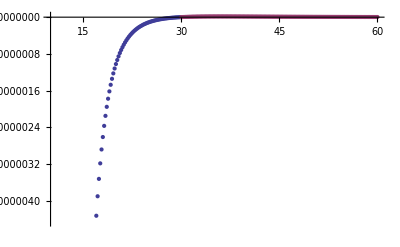

```mathematica
ListPlot[{t2l,t2r},Axes->True]
```

```mathematica
(*Real vs Radius*)
```

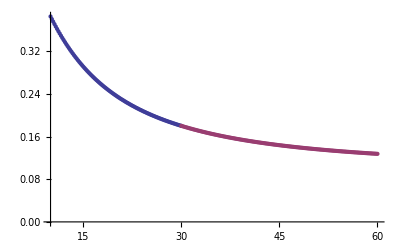

```mathematica
ListPlot[{t1l,t1r}]
```

```mathematica
Export["/home/h/skoli/pt/rnef/mathematica/mirror-radius/mu0.1/Q=0.95/q=0.25/R.dat",Join[t1l,t1r]]
Export["/home/h/skoli/pt/rnef/mathematica/mirror-radius/mu0.1/Q=0.95/q=0.25/I.dat",Join[t2l,t2r]]
```

/home/h/skoli/pt/rnef/mathematica/mirror-radius/mu0.1/Q=0.95/q=0.25/R.dat

/home/h/skoli/pt/rnef/mathematica/mirror-radius/mu0.1/Q=0.95/q=0.25/I.dat

```mathematica
(*This is for estimate the "Analytical" value using Cardoso's bomb *)
```

```mathematica
(*Radius*)
```

```mathematica
rp=M+Sqrt[M^2-Q^2]
rm=M-Sqrt[M^2-Q^2]
rmirror=40
```

1.6

0.4

40

```mathematica
(*Frequencies*)
```

```mathematica
wc=qscal*Q/rp
wtilde=(wa-wc)*(rp^2/(rp-rm))
```

0.45

2.13333 (-0.45+wa)

```mathematica
(*Nodes*)
```

```mathematica
n=0
```

0

```mathematica
(*First aproximation, the root of the Bessel function (has to be the n+1 root, otherwise the 1st is zero!)*)
```

```mathematica
jl12n=N[BesselJZero[l+1/2,n+1],10]
```

4.493409459

```mathematica
wfa=jl12n/rmirror
```

0.1123352365

```mathematica
(*Let's calculate the imaginary part, delta, we need some definitions in advance*)
```

```mathematica
Product[i^2+4*wtilde^2,{i,1,l}]
```

1+18.2044 (-0.45+wa)^2

```mathematica
gamm=(Factorial[l]/Factorial2[(2*l-1)])^2*rp^2*(rp-rm)^(2*l)/Factorial[2*l]/Factorial[2*l+1]*2/(2*l+1)*Product[i^2+4*wtilde^2,{i,1,l}]*jl12n^(2*l+1)
```

18.5805 (1+18.2044 (-0.45+wa)^2)

```mathematica
Dbess=D[BesselJ[l+1/2,x],x]/.x->jl12n
```

-0.367413504

```mathematica
f1=(-1)^(l)*BesselJ[-l-1/2,jl12n]/Dbess
```

1.049528

```mathematica
f2=(wfa-wc)/rmirror^(2*l+2)
```

-1.319×10^-7

```mathematica
(*Imaginary part delta*)
```

```mathematica
deltat=-gamm*f1*f2/.wa->wfa
```

7.91099×10^-6

```mathematica
(*make a list of the 1/r decay*)
```

```mathematica
tan=Table[jl12n/i,{i,50}];
```

```mathematica
(*Compare the behaviour of Re[w] in a plot*)
```



```mathematica
ListPlot[{t1l,t1r,tan}]
```